-Graphics-

## Using IFTTT and Data Drop

The IFTTT Wolfram Data Drop^™ Channel

Do Recipes

If Recipes

Arduino and the Raspberry Pi

SemanticImport and DatabinUpload

Data Drop Resources

## IFTTT: IF This Then That

IFTTT makes it possible to create simple connections between many everyday products, giving you creative control over products and apps.

#### Recipes

Recipes are simple connections between products and apps. There are two types.

DO Recipes

IF Recipes

-Graphics-

#### DO Recipes

DO Recipes run with a single tap, letting you create your own personalized Button, Camera, and Notepad. DO apps are available for iOS and Android.

#### IF Recipes

IF Recipes run in the background, creating connections with the statement “if this then that.”

## Creating a Wolfram Data Drop IF Recipe

#### Sign in to IFTTT

Sign in to https://ifttt.com. Go to My Recipes.

Click Create a Recipe.

-Graphics-

#### Step 1: Choose Trigger Channel

#### Step 2: Choose a Trigger

#### Step 3: Complete Trigger fields

#### Step 4: Choose Wolfram Data Drop as your action channel

#### Step 5: Select “Add entry” action

```mathematica
CreateDatabin[<|"Name"->"World's Zoos"|>,"Interpretation"->{"city"->"City","at"->"Date"}]
```

#### Step 6: Complete action fields

#### Step 7: Create and connect

## CloudBit from LittleBits

A cloudBit module with a sound trigger for notification adds an entry to a databin whenever the telephone is ringing.

-Graphics-

This extracts the data in the bin as a time series.

```mathematica
ts=TimeSeries[Databin["6COGRHn1"]]
```

<|input→TimeSeries[…]|>

Plotting the time series shows how often the telephone rings and when.

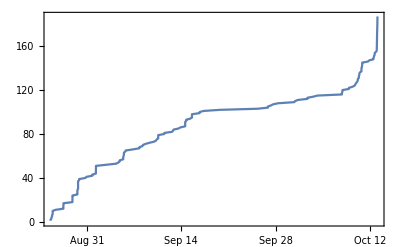

```mathematica
DateListPlot[Accumulate[TimeSeries[ts["input"],TemporalRegularity->True]]]
```

## The Netatmo Weather Station

The Netatmo Weather Station includes sensors for monitoring temperature, barometric pressure, humidity, carbon dioxide, noise pollution, and more. The app displays your station’s measurements using dashboards, graphs, and notifications.

#### Triggers

Air pressure rises above

Air pressure drops below

Target pressure

Carbon dioxide rises above

Carbon dioxide drops below

Target carbon dioxide

Humidity rises above

Humidity drops below

Target humidity percentage

Noise level rises above

Noise level drops below

Temperature rises above

Temperature drops below

Rain detected

Rain no longer detected

Today’s rainfall measurement

Yesterday’s rainfall measurement

#### Noise level rises above or drops below 50 dB

```mathematica
CreateDatabin[<|"Name"->"Netatmo"|>,"Interpretation"->{"noise"->Restricted["StructuredQuantity",IndependentUnit["decibels"]]}]
```

Databin[…]

-Graphics-

-Graphics-

```mathematica
noise=Databin["5vFGwnzi",Yesterday]
```

Databin[…]

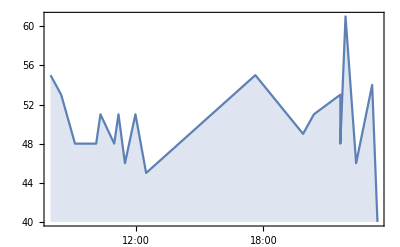

```mathematica
DateListPlot[noise,Filling->Bottom][[1]]
```

#### Wolfram|Alpha^® analysis

Data drop 5vFGwnzi

## SemanticImport and DatabinUpload

SemanticImport of data from a Netatmo personal weather station in Barcelona.

http://community.wolfram.com/groups/-/m/t/582196

## Arduino and the Raspberry Pi

#### Arduino Yún

Community example by Arnoud Buzing.

```mathematica
CreateDatabin[]
```

Arduino code.

```mathematica
#include <Bridge.h>

Process p;
int val,count;
float voltage,temperature,average;

void setup() {
 count=0;
 average=0;
 Bridge.begin();
 Serial.begin(9600);
}

void loop() {
 val = analogRead(0);
 voltage = val * 5.0;
 voltage = voltage/1024.0;
 temperature = (voltage-0.5)*100;
 average += temperature;
 count++;
 if( count>59 ) {
  p.begin("/usr/bin/curl");
  p.addParameter("--insecure");
  p.addParameter("--location");
  p.addParameter("https://datadrop.wolframcloud.com/api/v1.0/Add?bin=YOUR_BIN_ID&temperature="+String(average/60));
  p.run();
  while(p.available()>0) {
   char c = p.read();
   Serial.print(c);
  }
  Serial.println();
  Serial.flush();
  count = 0;
  average = 0;
 }
 delay(1000);
}
```

Analysis of the temperature data.

```mathematica
bin=Databin["YOUR_BIN_ID"];
data=bin["Data"];
temperature=data["temperature"]
```

#### Raspberry Pi

The Raspberry Pi is an inexpensive computer that plugs into a monitor or TV and uses a standard keyboard and mouse. It enables people of all ages to explore computing and learn to program.

#### Data Drop and a PIR motion sensor

One of the most useful things about using the Wolfram Language on the Pi is that it works seamlessly with the new Wolfram Data Drop open service. This allows you to make an activity tracker in just a few minutes. For example, using Data Drop and a PIR (passive infrared sensor) motion sensor, I kept track of all human movements in my hall for several months.

Every 20 minutes the total number of counts was added to a Databin, so I could monitor my hall in real time from anywhere with Wolfram|Alpha^®. And if I wanted to, I could also analyze the data and create advanced visualizations, like the one in the following DateListPlot that distinguishes business days from weekends.

```mathematica
activity = Databin["3v1UbpOM"]["Data"]["movements"]
```

EventSeries[…]

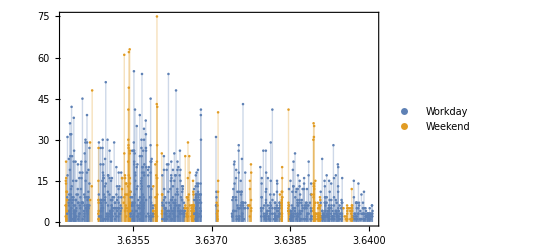

```mathematica
DateListPlot[{Select[activity["Path"],DayMatchQ[#[[1]],"BusinessDay"]&&#[[2]]>0&],
Select[activity["Path"],DayMatchQ[#[[1]],"Weekend"]&&#[[2]]>0&]}, Joined -> False, Filling -> Axis, PlotRange -> All,PlotLegends->{"Workday","Weekend"}]
```

#### How to make a time-lapse video with Raspberry Pi and Data Drop

The Wolfram Data Drop also accepts images from the Raspberry Pi camera module. So you can easily make a remote motion trigger with a PIR sensor.

-Graphics-

Whenever a movement is detected, it triggers the RaspiCam and sends the snapshot to the following databin.

Wolfram Community Tutorial

## Data Drop Resources

IFTTT.com

netatmo.com

#### Interesting Trigger Channels for Data Drop

littleBits

Wikipedia

Android Location

iOS Location

iOS Contacts

Feed

Reddit

Pinterest

Stocks

Weather

Chain

Fitbit

Netatmo

Facebook Pages

GitHub

Launch Center

GE Appliances GeoSpring^™

GE Appliances Cooking

GreenIQ

#### Tutorials

Quick and Easy Access to Your Mobile App Data by Bradley Ashby

Capturing Data from an Android Phone Using Wolfram Data Drop by Diego Zviovich

Track Everything with the Wolfram Data Drop IFTTT Channel!

Wolfram Data Drop IFTTT Channel: Track Your Elevation and Much More

SemanticImport of Data from a Netatmo Personal Weather Station in Barcelona

#### Arduino and the Raspberry Pi

Build Your Own Weather Station in a Snap with the Wolfram Cloud!

Wolfram + Raspberry Pi Project

Wolfram Data Drop Quick Reference

Raspberry Pi Group on Wolfram Community

Free Tutorial: Wolfram Language on Raspberry Pi

Wolfram Language Guide: Using Connected Devices

## RSVP Form

https://www.wolframcloud.com/objects/bernate/RSVPmovie

#### Preview

-Graphics-

#### Movie RSVP databin

```mathematica
CreateDatabin[<|"Name"->"RSVP Databin"|>,"Interpretation"->{
"first"->"String",
"last"->"String",
"email"->"String",
"institution"->"String",
"guests"->"Integer"}]
```

Databin[…]

### HTML responses

#### Thank you for your RSVP response

```mathematica
rsvpthankyou="<!DOCTYPE html>
<html lang=\"en\">
  <head>
    <meta charset=\"utf-8\">
    <meta http-equiv=\"X-UA-Compatible\" content=\"IE=edge\">
    <meta name=\"viewport\" content=\"width=device-width, initial-scale=1\">
    <!-- The above 3 meta tags *must* come first in the head; any other head content must come *after* these tags -->
    <meta name=\"author\" content=\"Wolfram Research\">

    <title>RSVP</title>

    <!-- Bootstrap -->
    <link href=\"https://www.wolframcloud.com/res/themes/css/white.min.css\" rel=\"stylesheet\">


  </head>

  <body class='body-default   '>


    <div class=\"site-wrapper\">
      <div class=\"site-wrapper-inner\">

          <!-- Begin page content -->
      <div id=\"content\" class=\"container container-main\">

<h2>
 Thank you for your RSVP to the exclusive screening of the Man Who Knew Infinity sponsored by Wolfram Research. Join us at 7pm&nbsp;&nbsp;Wednesday, May 4 at Carmike Cinema located at 910 Meijer Dr in Champaign, IL.<br /><br />Learn more about Srinivasa Ramanujan&rsquo;s legacy in Stephen Wolfram&rsquo;s most recent <span><a href=\"http://blog.stephenwolfram.com/2016/04/who-was-ramanujan\"><span class=\"HyperlinkInline\">blog</span></a></span>.
</h2>
<a href=\"http://gowatchit.com/microsite/2815\" target=\"_blank\"><img src=\"http://blog.stephenwolfram.com/data/uploads/2016/04/hardy-and-ramanujan-in-the-man-who-knew-infinity.png\" alt=\"&quot;Hardy&quot; and &quot;Ramanujan&quot; in The Man Who Knew Infinity\" title=\"&quot;Hardy&quot; and &quot;Ramanujan&quot; in The Man Who Knew Infinity\" width=\"620\" height=\"413\" class=\"alignnone size-full wp-image-11525\" /></a><span id=\"more-11518\"></span></p>

      </div>
    </div>
    </div>


    <!-- jQuery (necessary for Bootstrap's JavaScript plugins) -->
    <script src=\"https://ajax.googleapis.com/ajax/libs/jquery/1.11.3/jquery.min.js\"></script>
    <!-- Include all compiled plugins (below), or include individual files as needed -->
    <script defer=\"defer\" type=\"text/javascript\" src=\"https://www.wolframcloud.com/res/themes/js/app.min.js?v=1.31\"></script>
  </body>
</html>";
```

#### Waiting list response

```mathematica
waitinglist="<!DOCTYPE html>
<html lang=\"en\">
  <head>
    <meta charset=\"utf-8\">
    <meta http-equiv=\"X-UA-Compatible\" content=\"IE=edge\">
    <meta name=\"viewport\" content=\"width=device-width, initial-scale=1\">
    <!-- The above 3 meta tags *must* come first in the head; any other head content must come *after* these tags -->
    <meta name=\"author\" content=\"Wolfram Research\">

    <title>RSVP</title>

    <!-- Bootstrap -->
    <link href=\"https://www.wolframcloud.com/res/themes/css/white.min.css\" rel=\"stylesheet\">


  </head>

  <body class='body-default   '>


    <div class=\"site-wrapper\">
      <div class=\"site-wrapper-inner\">

          <!-- Begin page content -->
      <div id=\"content\" class=\"container container-main\">

<h2>
 Our free showing The Man Who Knew Infinity is now full. Thank you for registering, we will add your name to the waiting list and notify you should seats become available.<br /><br />Learn more about Srinivasa Ramanujan&rsquo;s legacy in Stephen Wolfram&rsquo;s most recent <span><a href=\"http://blog.stephenwolfram.com/2016/04/who-was-ramanujan\"><span class=\"HyperlinkInline\">blog</span></a></span>.
</h2>
<a href=\"http://gowatchit.com/microsite/2815\" target=\"_blank\"><img src=\"http://blog.stephenwolfram.com/data/uploads/2016/04/hardy-and-ramanujan-in-the-man-who-knew-infinity.png\" alt=\"&quot;Hardy&quot; and &quot;Ramanujan&quot; in The Man Who Knew Infinity\" title=\"&quot;Hardy&quot; and &quot;Ramanujan&quot; in The Man Who Knew Infinity\" width=\"620\" height=\"413\" class=\"alignnone size-full wp-image-11525\" /></a><span id=\"more-11518\"></span></p>

      </div>
    </div>
    </div>


    <!-- jQuery (necessary for Bootstrap's JavaScript plugins) -->
    <script src=\"https://ajax.googleapis.com/ajax/libs/jquery/1.11.3/jquery.min.js\"></script>
    <!-- Include all compiled plugins (below), or include individual files as needed -->
    <script defer=\"defer\" type=\"text/javascript\" src=\"https://www.wolframcloud.com/res/themes/js/app.min.js?v=1.31\"></script>
  </body>
</html>";
```

### RSVP Form

```mathematica
CloudDeploy[Delayed[FormFunction[{
{"first", "First Name"} -> "String",
{"last", "Last Name"} -> "String",
{"email", "Email"} -> "EmailAddress",
{"institution","Company/Institution"}->"String",
{"guests","Guests (+3 max)"}-><|"Interpreter"->{0->0,1->1,2->2,3->3}, "Control" -> RadioButtonBar|>}
, 
ExportForm[
(DatabinAdd[Databin["gBc171Hy"],<|"first"->#first,"last"->#last,"email"->#email,"institution"->#institution,"guests"->(1+#guests)|>];
attendees=(300-Total[Databin["gBc171Hy"]["Values"]["guests"]]);
If[attendees>1,rsvpthankyou,waitinglist]),"HTML"]&
,
AppearanceRules-> <|"Title" -> "Wolfram Research is pleased to present a private screening of The Man Who Knew Infinity on Wednesday, May 4th at 7pm at the Carmike Cinemas.", 
"Description" -> (attendees=(300-Total[Databin["gBc171Hy"]["Values"]["guests"]]);
If[attendees>1,
"Please RSVP (only "<>ToString[attendees]<>" spots available):",
"Tickets to The Man Who Knew Infinity are now sold out. Thank you for registering, we will add your name to the waiting list and notify you should seats become available"])|>]],
"RSVPmovie",Permissions->"Public"]
```

CloudObject[]

#### RSVP List:

```mathematica
data=Normal[Normal[Databin["gBc171Hy"]["Dataset"]]][[All,1;;-2,2]];
Text@Grid[Prepend[data,{"First Name","Last Name","e-mail","Institution","N.ba"}],
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},
Alignment->{{{Left}}},ItemSize->{{8,10,14,20,1.5}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

First Name | Last Name | e-mail | Institution | N.ba
Bernat | Espigule | bernate@wolfram.com | Wolfram | 4
John | Muir | john@yahoo.com | Yahoo | 3

## Teach Wolfram Alpha Your Sense of Humor

teachwolframalpha.com

#### Preview

-Graphics-

### Admin Tools

#### Databins for collecting questions and answers:

```mathematica
binq=CreateDatabin[<|"Name"->"WA Humor Questions"|>]
```

Databin[…]

```mathematica
bina=CreateDatabin[<|"Name"->"WA Humor Answers"|>]
```

Databin[…]

```mathematica
binh=CreateDatabin[<|"Name"->"Hidden Questions"|>]
```

Databin[…]

#### Add new question:

```mathematica
binq = Databin["gCI827qk"];
binh = Databin["gCIdfxq9"];
CloudDeploy[FormFunction[{{"questions", ""} -> RepeatingElement[<|"Interpreter" -> "String"|>, {{i, 1}, {1, 15}}]},
  (
  (* DatabinUpload new questions *)
  DatabinUpload[binq, #questions];
  (* Add new questions to the hidden questions list *)
  DatabinAdd[binh, Join[First@Values[binh[-1]], #questions]];
  (* Redirect to hidequestions Form *)
  HTTPRedirect["https://www.wolframcloud.com/objects/bernate/wahumor/unhidequestions"]
  ) &, AppearanceRules -> <|"Title" -> "Add new questions"|>, FormTheme -> "Blue"], 
  "wahumor/addquestions", Permissions -> "Public"]
```

CloudObject[]

#### SendMail NOREPLY:

```mathematica
CloudDeploy[APIFunction[{"question"->"String","answer"->"String","email"->"String"->"test@wolfram.com"},SendMail[#email,{"Wolfram|Alpha--thanks for the joke!",TemplateApply[StringTemplate["We want to thank you for submitting your answer to Wolfram|Alpha and helping to teach it a sense of humor!

`1`

`2`

Wolfram|Alpha will assess your response, and if your witty answer becomes part of Wolfram|Alpha's repertoire, we will let you know! 

Sincerely,

The Wolfram|Alpha team"], {#question, #answer}]}]&],"sendmail",Permissions->"Public"]
```

CloudObject[]

#### Template:

```mathematica
template="<!doctype html>
<html>
<head>
    <meta charset=\"utf-8\">
    <title>Teach Wolfram|Alpha Your Sense of Humor</title>
    <meta name=\"viewport\" content=\"width=device-width,initial-scale=1,maximum-scale=1\">    
<meta name=\"description\" content=\"Contribute your wit and help Wolfram|Alpha tell better jokes and become an even smarter AI. A Wolfram Cloud site.\">
<!-- for Google -->
<meta name=\"keywords\" content=\"Wolfram|Alpha, humor, Wolfram, WA, AI, teach, jokes\" />
<meta name=\"author\" content=\"Wolfram|Alpha\" />
<meta name=\"copyright\" content=\"Wolfram Research\" />
<meta name=\"application-name\" content=\"Teach Wolfram|Alpha Your Sense of Humor\" />

<!-- for Facebook -->          
<meta property=\"og:title\" content=\"Teach Wolfram|Alpha Your Sense of Humor\" />
<meta property=\"og:type\" content=\"website\" />
<meta property=\"og:image\" content=\"https://www.wolframcloud.com/objects/microsites/wahumor/img/teachwahumor.png\" />
<meta property=\"og:url\" content=\"http://teachwolframalpha.com\" />
<meta property=\"og:description\" content=\"Contribute your wit and help Wolfram|Alpha tell better jokes and become an even smarter AI. A Wolfram Cloud site.\" />

<!-- for Twitter -->          
<meta name=\"twitter:card\" content=\"Contribute your wit and help Wolfram|Alpha tell better jokes and become an even smarter AI. A Wolfram Cloud site.\" />
<meta name=\"twitter:title\" content=\"Teach Wolfram|Alpha Your Sense of Humor\" />
<meta name=\"twitter:description\" content=\"http://teachwolframalpha.com\" />
<meta name=\"twitter:image\" content=\"https://www.wolframcloud.com/objects/microsites/wahumor/img/teachwahumor.png\" />
    
    <link href='https://fonts.googleapis.com/css?family=Source+Sans+Pro:400,600,300italic,400italic,600italic,300|Roboto:400,300,300italic,100italic,100,400italic,500,500italic' rel='stylesheet' type='text/css'>
    <link href=\"styles.css\" rel=\"stylesheet\" type=\"text/css\" media=\"screen\">
    <script src=\"https://code.jquery.com/jquery-3.0.0.min.js\" integrity=\"sha256-JmvOoLtYsmqlsWxa7mDSLMwa6dZ9rrIdtrrVYRnDRH0=\" crossorigin=\"anonymous\"></script>
    <script src=\"https://cdnjs.cloudflare.com/ajax/libs/jquery-validate/1.15.0/jquery.validate.min.js\" integrity=\"sha384-vilVZsMIwXgPUnHQKsriY2wkMmSqqbHRst8+6uxPrtHdZQaejD+yHzdnNzH8+duW\" crossorigin=\"anonymous\"></script>    
    <script>jQuery(document).ready(function () { 

\tjQuery('.questions p').click(function() {
\t\tvar questionText = jQuery(this).text();
\t\tjQuery('body').toggleClass('popup');
\t\tjQuery('#popup .title').text(questionText);
\t\tjQuery('#hiddenquestion').val(questionText);
\t\tjQuery('#popup').toggle();
\t});
\tjQuery('.closex').click(function() {
\t\tjQuery('body').toggleClass('popup');
\t\tjQuery('#answer').val('');
\t\tjQuery('#comments').val('');
\t\tjQuery('#popup').hide();
\t\tjQuery('#thankspopup').hide();
\t});\t\t
\tjQuery('.closex-justthis').click(function() {\t\t
\t\tjQuery('#privacy').hide();\t\t
\t\tjQuery('#popup').show();
\t});

\tjQuery( \"#submitForm\" ).submit(function( event ) {
\t\t// Stop form from submitting normally
\t\tevent.preventDefault();
\t\t
\t\t// Get some values from elements on the page:
\t\tvar theForm = jQuery( this ),
\t\tquestionval = theForm.find( \"input[name='Question']\" ).val(),
\t\tanswerval = theForm.find( \"textarea[name='Answer']\" ).val(),
\t\tcommentsval = theForm.find( \"input[name='Comments']\" ).val(), 
\t\temailval =  theForm.find( \"input[name='Email']\" ).val(),
\t\t
\t\turl = 'https://datadrop.wolframcloud.com/api/v1.0/Add?bin=<wolfram:slot id='binaURL'/>&question='+questionval+'&answer='+answerval+'&comments='+commentsval+'&email='+emailval;
\t\teurl = 'https://www.wolframcloud.com/objects/bernate/sendmail?question='+questionval+'&answer='+answerval+'&email='+emailval;
\t\tvar validator = jQuery( this ).validate();
\t\t
\t\tif ( (validator.element( \"#answer\" )) && (validator.element( \"#email\" ))) {
\t\t\t// Send the data using post
\t\t\tvar posting = jQuery.post( url, { question:questionval, answer:answerval, comments:commentsval, email:emailval } );
\t\t\t// Send a thank you email
\t\t\tvar eposting = jQuery.post( eurl, { question:questionval, answer:answerval, email:emailval } );
\t\t\t
\t\t\t
\t\t\tjQuery('#popup').css('opacity',0.5);
\t\t\t
\t\t\t// Display thank you div
\t\t\tposting.done(function() {
\t\t\t\tjQuery('#popup').hide();
\t\t\t\tjQuery('#answer').val('');
\t\t\t\tjQuery('#comments').val('');
\t\t\t\tjQuery('#thankspopup').show();
\t\t\t\tjQuery('#popup').css('opacity',1);
\t\t\t});
\t\t}
\t\t
\t\t});\t\t
\t\t\t
\tjQuery('#privacylink').click(function() {\t\t
\t\tjQuery('#privacy').show();\t\t
\t\tjQuery('#popup').hide();\t\t
\t\treturn false;
\t});

});</script>
</head>

<body>
\t<div id=\"content\">
        <div id=\"header\">
            <div class=\"container center\">
                <div class=\"logo\"><img src=\"img/logo.png\" alt=\"Teach WolframAlpha your sense of humor\" /></div>
            </div>
        </div>
        <div id=\"main\">
          <div class=\"container\">
              <p><strong>Q: Why did the computational knowledge engine cross the road?</strong><br>
              <strong class=\"gray\">A: To learn some better jokes. </strong></p>
              <p>Wolfram|Alpha's knowledge about the world is constantly growing, and it wants to grow its sense of humor too. But what do humans find funny? Wolfram|Alpha needs your help to figure that out...</p>
              <p class=\"orange-tilt fortytop\">Pick a question and give the wittiest answer you can...</p>
              
              <div class=\"questions\">
                <wolfram:slot id='q'/>
            </div>
             
             <div id=\"mainshare\">
             \t<span>#WolfAI</span>
             \t\t<a target=\"_blank\" href=\"https://www.facebook.com/sharer/sharer.php?t=Teach+Wolfram%7CAlpha+Your+Sense+of+Humor&u=http%3a%2f%2fteachwolframalpha.com\" class=\"shareicon\"><img src=\"img/icon-fb.png\" width=\"35\" height=\"35\" alt=\"Share on Facebook\"></a>
                    <a target=\"_blank\" href=\"https://twitter.com/intent/tweet?text=Teach+Wolfram%7CAlpha+Your+Sense+of+Humor+%23WolfAI&amp;url=http%3a%2f%2fteachwolframalpha.com\" class=\"shareicon\"><img src=\"img/icon-twitter.png\" width=\"35\" height=\"35\" alt=\"Share on twitter\"></a>
                    <a target=\"_blank\" href=\"http://www.reddit.com/submit?url=http%3a%2f%2fteachwolframalpha.com&title=Teach+Wolfram%7CAlpha+Your+Sense+of+Humor\" class=\"shareicon\"><img src=\"img/icon-reddit.png\" width=\"35\" height=\"35\" alt=\"Share on Reddit\"></a>
                    <a target=\"_blank\" href=\"mailto:?subject=Teach%20Wolfram%7CAlpha%20Your%20Sense%20of%20Humor&body=Teach%20Wolfram%7CAlpha%20Your%20Sense%20of%20Humor:%0d%0a%0d%0ahttp%3a%2f%2fteachwolframalpha.com\" class=\"shareicon\"><img src=\"img/icon-email.png\" width=\"35\" height=\"35\" alt=\"Share via Email\"></a>
             </div>
              
          </div>
        </div>
        <div id=\"footer\">
            <div class=\"container center\">              
                <ul id=\"menu-bottom-menu\" class=\"text-center\">
                    <li class=\"powered-link\"><a href=\"https://www.wolframcloud.com/\">Powered by the Wolfram Cloud</a></li>
                    <li><a href=\"http://wolfram.com\">Wolfram.com</a></li>
                    <li><a href=\"http://wolframalpha.com\">WolframAlpha.com</a></li>
                    <li><a href=\"http://www.wolfram.com/resources/\">All Wolfram Sites</a></li>
                </ul> 
                            
                <ul id=\"menu-small-footer-menu\" class=\"text-center\">
                    <li><a href=\"http://wolfram.com\">© 2016 Wolfram Research, Inc.</a></li>
                    <li><a target=\"_blank\" href=\"https://www.wolfram.com/legal/terms/wolfram-cloud.html\">Terms of Use</a></li>
                    <li><a target=\"_blank\" href=\"http://wolfram.com/legal/privacy/wolfram-cloud.html\">Privacy Policy</a></li>
                    <li><a href=\"http://www.wolfram.com/company/contact/general/\">Contact Us</a></li>
                </ul> 
            </div>
        </div>
    </div>
    
<div id=\"popup\">
    <form id=\"submitForm\" action=\"/\" method=\"post\">
        <div class=\"content\">
          <div class=\"closex unselectable x\">&#10799;</div>
          <div class=\"title\"></div>
            <div class=\"formelements\">
                <input id=\"hiddenquestion\" name=\"Question\" type=\"hidden\" value=\"000\">
                <p><textarea id=\"answer\" name=\"Answer\" rows=\"6\" maxlength=\"300\" placeholder=\"What's your wittiest answer? (Max 300 characters.)\" required></textarea><span class=\"tinytext\">By submitting this, you're giving Wolfram|Alpha the <a id=\"privacylink\" class=\"textlink\" href=\"\">right to use</a> what you write in any way.</span></p>
               <p><label>Your email <span class=\"tinytext\">(optional)</span>:</label><br><input id=\"email\" name=\"Email\" type=\"email\"><span class=\"tinytext\">If you don't tell us your email, we won't be able to tell you if we use your answer.</span></p>
               <p><label>Comments for the Wolfram|Alpha team:</label><br><textarea id=\"comments\" name=\"Comments\" rows=\"3\" maxlength=\"300\"></textarea></p>
               
          </div>
        </div>
        <div class=\"popupfooter\"><input type=\"submit\" value=\"Submit\"></div>
    </form>
</div>

</body>
</html>
";
```

#### Display questions:

```mathematica
binq = Databin["gCI827qk"];
bina = Databin["gCIa9khv"];
binh = Databin["gCIdfxq9"];
keys=StringJoin/@Tuples[{Alphabet[],Alphabet[],Alphabet[]}];
CloudDeploy[Delayed[FormFunction[
questions=Values[binq];
hiddenquestions=First@Values[binh[-1]];
Table[{keys[[i]],""}-><|"Interpreter"->"Boolean","Default"->!MemberQ[hiddenquestions,questions[[i]]],"Help" ->questions[[i]]|>,{i,Length[questions]}],
((* CloudDeploy questions (unselected) *)
CloudDeploy[ExportForm[TemplateApply[
XMLTemplate[template],
<|"q"->StringJoin["<p>"<>#<>"</p>
"&/@Pick[questions,Boole[Values[#]],1]],
"binaURL"->bina["ShortID"]|>],
"HTML"],
"wahumor/questions",Permissions->"Public"];
(* Data drop hidden questions (selected) *)
DatabinAdd[binh,Pick[questions,Boole[Values[#]],0]];
(* Redirect to new questions page *)
HTTPRedirect["https://www.wolframcloud.com/objects/bernate/wahumor/questions"])&,
AppearanceRules-><|"Title" -> "Select questions to be displayed"|>,FormTheme->"Blue"]],
"wahumor/unhidequestions", Permissions->"Public"]
```

CloudObject[]

#### Hide questions:

```mathematica
binq = Databin["gCI827qk"];
bina = Databin["gCIa9khv"];
binh = Databin["gCIdfxq9"];
keys=StringJoin/@Tuples[{Alphabet[],Alphabet[],Alphabet[]}];
CloudDeploy[Delayed[FormFunction[
questions=Values[binq];
hiddenquestions=First@Values[binh[-1]];
Table[{keys[[i]],""}-><|"Interpreter"->"Boolean","Default"->MemberQ[hiddenquestions,questions[[i]]],"Help" ->questions[[i]]|>,{i,Length[questions]}],
((* CloudDeploy questions (unselected) *)
CloudDeploy[ExportForm[TemplateApply[
XMLTemplate[template],
<|"q"->StringJoin["<p>"<>#<>"</p>
"&/@Pick[questions,Boole[Values[#]],0]],
"binaURL"->bina["ShortID"]|>],
"HTML"],
"wahumor/questions",Permissions->"Public"];
(* Data drop hidden questions (selected) *)
DatabinAdd[binh,Pick[questions,Boole[Values[#]],1]];
(* Redirect to new questions page *)
HTTPRedirect["https://www.wolframcloud.com/objects/bernate/wahumor/questions"])&,
AppearanceRules-><|"Title" -> "Select questions to be hidden"|>,FormTheme->"Blue"]],
"wahumor/hidequestions", Permissions->"Public"]
```

CloudObject[]

## Microsites Resources

Cloud Functions & Deployment

### How it works: list of Microsites

Project Generator Project

Family Tour

MYPIDAY.COM

Image Identification Project

Celebrity Match

Code Cards Callery (Experimental)

Wolfram Community: Cloud

Darwin app

#### My Blog Posts about Data:

A Smart Programming Language for a Smart Cities Hackathon  May 1, 2015

Embrace the Maker Movement with the Raspberry Pi 2  June 18, 2015

Track Everything with the Wolfram Data Drop IFTTT Channel!  Sept 14, 2015

A Year of Runkeeper: Analysis and Visualization  December 4, 2015

Finding Pokémon GO’s Shortest Tour to Compute ‘em All! August 12, 2016